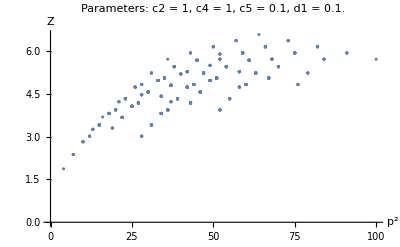

```mathematica
c2 = 1; 
c4 = 1; 
c5 = .1; 
d1 = .1;
L = 16;
Z[μ_] := 1;
Zhyp[ρ_] := Z[ρ . ρ] + c2 * (ρ . ρ) + c4 * (ρ[[1]]^4 + ρ[[2]]^4 + ρ[[3]]^4 + ρ[[4]]^4) / (ρ . ρ) + c5 * (ρ . ρ) * Log[ρ . ρ] + d1 / (ρ . ρ);
ptwid[p1_, p2_, p3_, p4_] := {Sin[2*Pi * p1 / L], Sin[2*Pi*p2 / L], Sin[2*Pi*p3/L], Sin[2*Pi*p4/L]};
Ztable = Table[{i^2 + j^2 + k^2 + l^2, Zhyp[ptwid[i, j, k, l]]},
 {i, 1, 5}, {j, 1, 5}, {k, 1, 5}, {l, 1, 5}];
Zlist = Flatten[Ztable, 3];
ListPlot[Zlist, AxesLabel->{p^2, Z}, PlotLabel->StringForm["Parameters: c2 = ``, c4 = ``, c5 = ``, d1 = ``. ",  c2, c4, c5, d1]]
```